# NewMazePaclet

XXXX | XXXX
XXXX | XXXX
XXXX | XXXX

XXXX.

Create a grid graph.

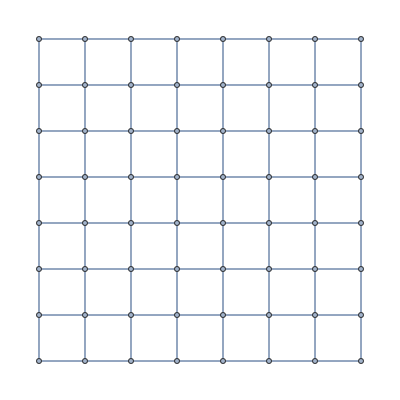

```mathematica
gridGraph=GridGraph[{8,8}]
```

Create a triangular grid graph.

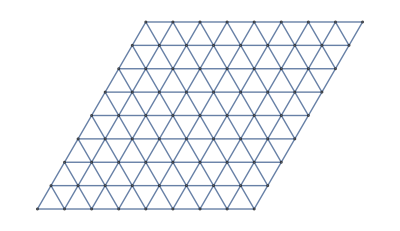

```mathematica
triangularGridGraph=TriangularGridGraph[{8,8}]
```

Create a hexagonal graph.

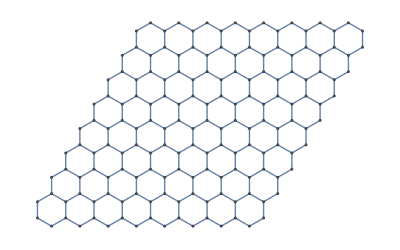

```mathematica
hexagonalGridGraph=HexagonalGridGraph[{8,8}]
```

Make a maze for each type of grid.

square grid:

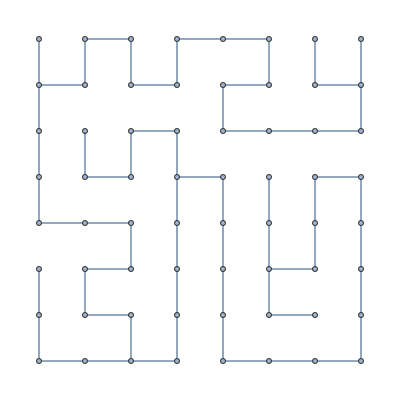

```mathematica
gridMaze=MakeMaze[gridGraph]
```

Triangular grid:

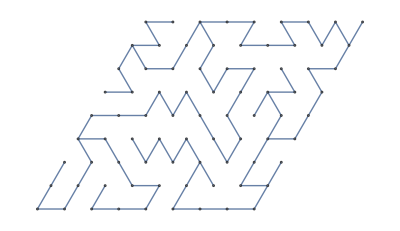

```mathematica
triangularMaze=MakeMaze[triangularGridGraph]
```

Hexagonal grid:

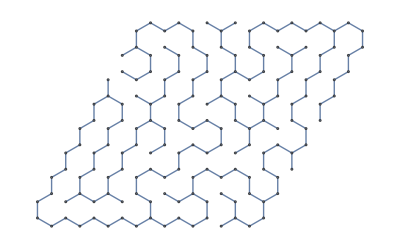

```mathematica
hexagonalMaze=MakeMaze[hexagonalGridGraph]
```

The main function of the paclet is SolveMaze. Solve the mazes.

Square maze solution:

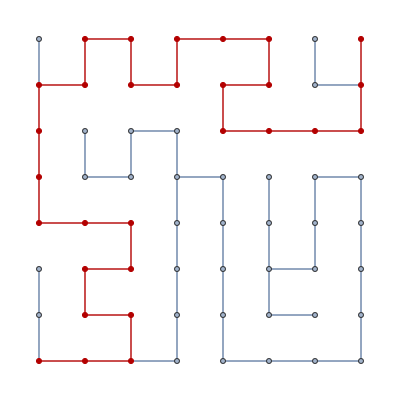

```mathematica
squareMazeSolution=SolveMaze[gridMaze]
```

Triangular maze solution:

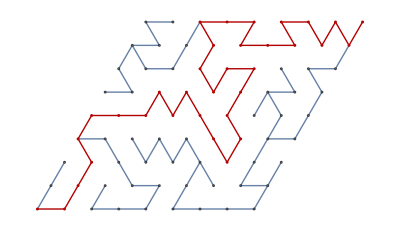

```mathematica
triangularMazeSolution=SolveMaze[triangularMaze]
```

Hexagonal maze solution:

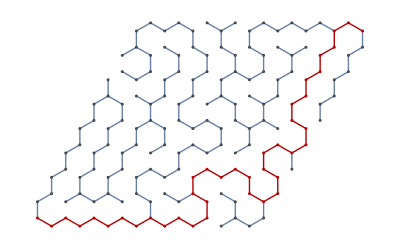

```mathematica
hexagonalMazeSolution=SolveMaze[hexagonalMaze]
```

There's also a function that will generate an equilateral triangle.

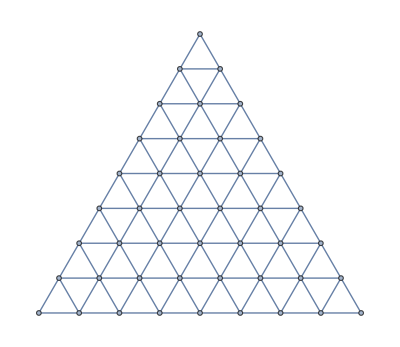

```mathematica
equilateralTriangleGraph=EquilateralTriangleGraph[8]
```

Make a maze:

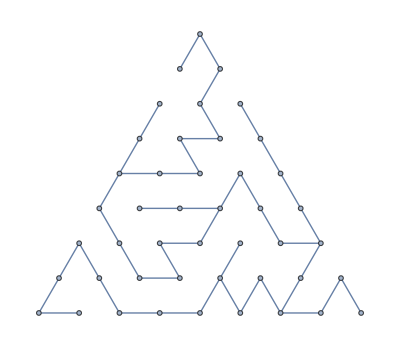

```mathematica
equilateralTriangleMaze=MakeMaze[equilateralTriangleGraph]
```

Solve the maze:

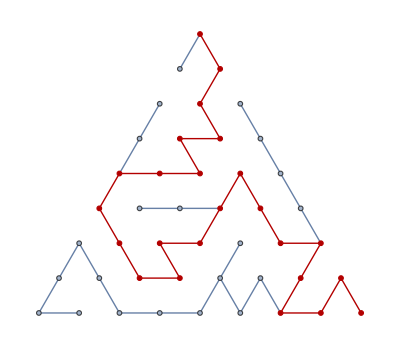

```mathematica
equilateralTriangleMaze=SolveMaze[equilateralTriangleMaze]
```

The problem with this function is it doesn't regularly tile the plane. You can't specify a different width and height, which you can do with TriangularGridGraph.

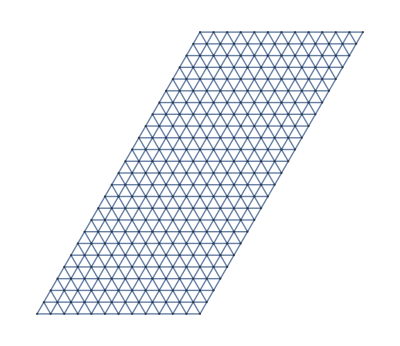

```mathematica
TriangularGridGraph[{12,24}]
```

You can only generate a 12 equilateral triangle or a 24 equilateral triangle.

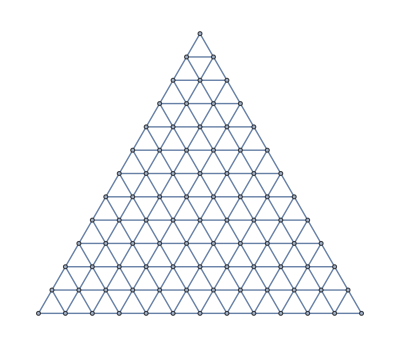

```mathematica
EquilateralTriangleGraph[12]
```

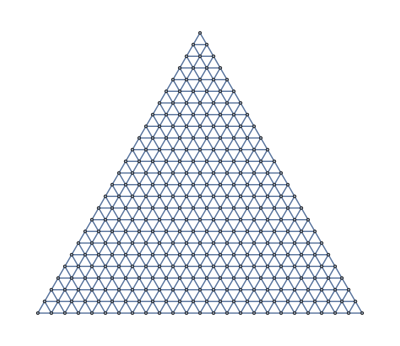

```mathematica
EquilateralTriangleGraph[24]
```

You can represent a maze with a tree:

```mathematica
GraphTree[triangularMaze]
```

-Graphics-

You can contract the edges of the tree of the graph.

A maze is an acyclic tree. Reduce the graph.

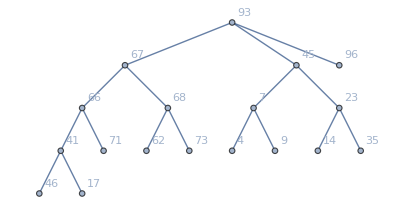

```mathematica
ReduceGraph[triangularMaze]
```

Related Guides

Mazes

Related Tech Notes

## Metadata

### Categorization

Tech Note

PeterBurbery/NewMazePaclet

PeterBurbery`NewMazePaclet`

PeterBurbery/NewMazePaclet/tutorial/NewMazePaclet

### Keywords